# Least Squares Solutions to Linear Systems

Let’s first just go through an example in an adhoc manner. We will then design a module to find a best fit polynomial to a dataset.

First we define the matrix X. Remember the first column of X is all 1’s and the second column is the x-coordinates of the dataset.

```mathematica
Xp={{1,1,1,1,1,1,1,1,1,1},{1,2,3,4,5,6,7,8,9,10}};
X=Transpose[Xp];
X//MatrixForm
```

(1 | 1
1 | 2
1 | 3
1 | 4
1 | 5
1 | 6
1 | 7
1 | 8
1 | 9
1 | 10)

The vector y is simply the y-coordinates of the data.

```mathematica
y={1.3,3.5,4.2,5.0,7.0,8.8,10.1,12.5,13.0,15.6};
y//MatrixForm
```

(1.3
3.5
4.2
5.
7.
8.8
10.1
12.5
13.
15.6)

Note that the equation Ax=y has no solution!

```mathematica
LinearSolve[X,y]
```

LinearSolve::nosol: Linear equation encountered that has no solution.

LinearSolve[{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10}},{1.3,3.5,4.2,5.,7.,8.8,10.1,12.5,13.,15.6}]

But, there is a unique least squares solution.

```mathematica
Coef=LinearSolve[Transpose[X].X,Transpose[X].y]
```

{-0.36,1.53818}

Note that Mathematica is happy to find a least squares solution for you.

```mathematica
LeastSquares[X,y]
```

{-0.36,1.53818}

They agree!

Now let’s plot the data as well as the least squares line.

```mathematica
Data=Table[{X[[i,2]],y[[i]]},{i,1,10}];
```

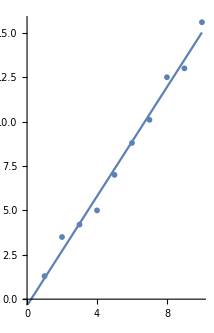

```mathematica
Show[{ListPlot[Data],Plot[Coef[[1]]+Coef[[2]]*x,{x,0,10}]},AspectRatio->Automatic]
```

This looks pretty good! It is interesting to compare this to the result in Example 1 on page 500 of our book. The least squares line is the same, but the method used in the book is based on solving the error minimization process using calculus.

## A General Least Square Polynomial Fit

Consider the following dataset that came from measuring the height of a projectile at time t. So, the data has the form (time, height).

```mathematica
Data={{0,0},{0.5,20.5},{1,31.36},{1.5,36.25},{2,30.41},{2.5,28.23}};
```

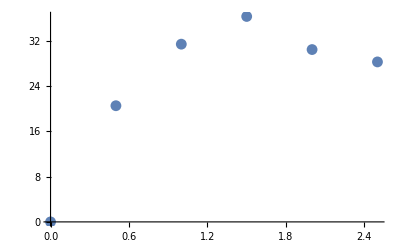

```mathematica
ListPlot[Data]
```

This is clearly not linear data. It (basically) looks like a parabola. In fact, if you remember vertical motion from physics, we know that the height function is quadratic in time. This is the kind of analysis you should do in order to decide what degree polynomial you want to fit.

We could certainly do this in a adhoc manner as we did before, but it seems more fun to design a Mathematica module that will fit a degree n polynomial to a given dataset.

```mathematica
PolyFit[Data_,deg_,var_]:=Module[{X,Xp,Coefs},
Xp=Join[{Table[1,{i,1,Length[Data]}]},Table[Table[Data[[i,1]]^(j),{i,1,Length[Data]}],{j,1,deg}]];
X=Transpose[Xp];
y=Table[Data[[i,2]],{i,1,Length[Data]}];
Coefs=LinearSolve[Transpose[X].X,Transpose[X].y];
Sum[Coefs[[i]]var^(i-1),{i,1,deg+1}]
];
```

```mathematica
p=PolyFit[Data,2,x]
```

1.17714+42.2226 x-12.8714 x^2

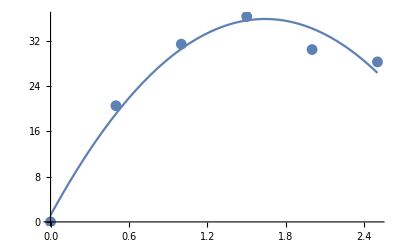

```mathematica
Show[ListPlot[Data],Plot[p,{x,0,2.5}]]
```

This looks pretty good! As we have mentioned, there is nothing in the math to tell you what degree polynomial you should fit. So, we could fit a polynomial of any degree... let’s take a look.

```mathematica
Manipulate[Show[ListPlot[Data],Plot[PolyFit[Data,n],{x,0,2.5}]],{n,1,6,1}]
```

LinearSolve::luc: Result for LinearSolve of badly conditioned matrix {{6., 7.5, 13.75, 28.125, 61.1875, 138.281, 320.547}, « 5 », {320.547, 756.445, 1808.51, « 15 », « 17 », 25977.4, 63831.4}} may contain significant numerical errors.

Hmm... what’s going on when we fit a degree 5 polynomial... why?